```mathematica
SetDirectory["/home/ethan/spring20/comphys/week4/coding"];
```

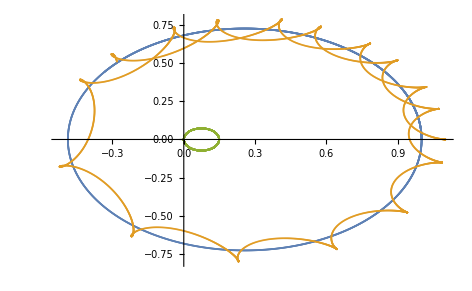

```mathematica
(* Name   dt         T      m0    x0    y0   vx0   vy0   m1      x1    y1    vx1   vy1       m2          x2      y2    vx2   vy2*)
data = Partition[ReadList[  "!./nbody 0.0003     1     1     0      0    0   -.5283 0.1     1     0     0     5.283     0.00001     1.1     0     0     0", Number], 13];
ListPlot[{data[[All, {4,5} ]], data[[All, {6,7}]], data[[All, {2,3}]]}]
```